```mathematica
T[centerdist_, rpulley_]:= 2 * Sqrt[(centerdist/2)^2 - rpulley^2];
TempPulleyAngle[centerdist_, rpulley_]:= ArcCos[rpulley/(centerdist / 2)];
LeadPulleyAngle[armdist_, centerdist_, rpulley_]:= 2*Pi - (Pi/2 + ArcSin[(armdist)/centerdist] + TempPulleyAngle[centerdist, rpulley] + Pi/2);
LeadPulleyAngleDiff[armdist_, centerdist_, rpulley_]:= Pi/2 - TempPulleyAngle[centerdist, rpulley] ;
ArmPulleyAngle[lacd_, adcd_, ldcd_, rpulley_ ]:= 2*Pi - (ArcCos[(lacd^2 + adcd^2 - ldcd^2)/(2*lacd * adcd)] + TempPulleyAngle[lacd, rpulley] + TempPulleyAngle[adcd, rpulley]);
ArmPulleyAngleDiff[lacd_, adcd_, ldcd_, rpulley_ ]:= ArcCos[(lacd^2 + adcd^2 - ldcd^2)/(2*lacd * adcd)] -(TempPulleyAngle[lacd, rpulley] + TempPulleyAngle[adcd, rpulley]);
ArmPulleyAngleDiff2[lacd_, adcd_, ldcd_, rpulley_ ]:= 2*Pi - ArcCos[(lacd^2 + adcd^2 - ldcd^2)/(2*lacd * adcd)] -(TempPulleyAngle[lacd, rpulley] + TempPulleyAngle[adcd, rpulley]);
CenterDist[α_, armlength_, xdiff_, heightdiff_]:=Sqrt[(armlength * Sin[α] - heightdiff)^2 + (armlength * Cos[α] - xdiff)^2];
TakeupSide[α_,armlength_,leaderx_,leadery_, armx_,army_, rpulley_]:= T[CenterDist[α, armlength, armx - leaderx, army + leadery], rpulley] + T[CenterDist[α, armlength, armx, army], rpulley] + rpulley * LeadPulleyAngle[Cos[α]*armlength - (armx - leaderx), CenterDist[α, armlength, armx - leaderx, army + leadery], rpulley]+ rpulley * ArmPulleyAngle[CenterDist[α, armlength, armx - leaderx, army + leadery], CenterDist[α, armlength, armx, army], leaderx, rpulley] - leaderx;
TakeupSideDiff[α_,armlength_,leaderx_,leadery_, armx_,army_, rpulley_]:= T[CenterDist[α, armlength, armx - leaderx, army + leadery], rpulley] + T[CenterDist[α, armlength, armx, army], rpulley] + rpulley * ArmPulleyAngleDiff[CenterDist[α, armlength, armx - leaderx, army + leadery], CenterDist[α, armlength, armx, army], Sqrt[leaderx^2 + leadery^2], rpulley] - leaderx+rpulley * (LeadPulleyAngleDiff[Cos[α]*armlength - (armx - leaderx), CenterDist[α, armlength, armx - leaderx, army + leadery], rpulley] - ArcSin[(leadery + army - armlength * Sin[α])/CenterDist[α, armlength, armx - leaderx, army + leadery]]);
TakeupSideDiff2[α_,armlength_,leaderx_,leadery_, armx_,army_, rpulley_]:= T[CenterDist[α, armlength, armx - leaderx, army + leadery], rpulley] + T[CenterDist[α, armlength, armx, army], rpulley] + rpulley * ArmPulleyAngleDiff2[CenterDist[α, armlength, armx - leaderx, army + leadery], CenterDist[α, armlength, armx, army], leaderx, rpulley] - leaderx+rpulley * (LeadPulleyAngleDiff[Cos[α]*armlength - (armx - leaderx), CenterDist[α, armlength, armx - leaderx, army + leadery], rpulley] - ArcSin[(leadery + army - armlength * Sin[α])/CenterDist[α, armlength, armx - leaderx, army + leadery]]);
Takeup[α_,β_, armlength_,leaderx_,leadery_, armx_,army_, rpulley_]:=TakeupSide[β,armlength,leaderx,leadery, armx,army, rpulley] + TakeupSide[α,armlength,leaderx,leadery, armx,army, rpulley];
```

```mathematica
larm= 0.25;
xleader=0.2;
yleader=0.015;
xarm=0.3542;
yarm=0.11;
rpulley = 0.02;
```

```mathematica
TakeupSide[1.038457189618663, larm, xleader, yleader, xarm, yarm, rpulley] + TakeupSide[1.0400587837476643, larm, xleader, yleader, xarm, yarm, rpulley]
```

0.474743

```mathematica
LeadPulleyAngleDiff[Cos[28.889* Pi /180]*larm - (xarm - xleader), CenterDist[28.889* Pi /180, larm, xarm - xleader, yarm + yleader], rpulley] - ArcSin[(yleader + yarm - larm * Sin[28.889 * Pi / 180])/CenterDist[28.889 * Pi / 180, larm, xarm - xleader, yarm + yleader]]
```

0.599795

```mathematica
ArmPulleyAngleDiff2[CenterDist[28.889* Pi/180, larm, xarm - xleader, yarm + yleader], CenterDist[28.889 * Pi/180, larm, xarm, yarm], Sqrt[xleader^2 + yleader^2], rpulley]*180/Pi
```

56.0587

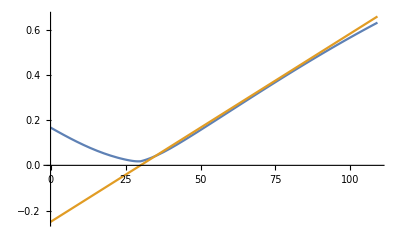

```mathematica
Plot[{TakeupSide[a* Pi /180,larm, xleader, yleader, xarm, yarm, rpulley], a * 0.00833333333 - .25}, {a, 0, 109}]
```

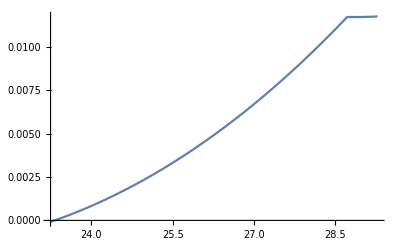

```mathematica
Plot[TakeupSideDiff[a* Pi /180,larm, xleader, yleader, xarm, yarm, rpulley], {a, 23.25, 29.275}]
```

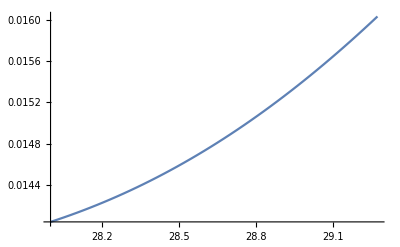

```mathematica
Plot[TakeupSideDiff2[a* Pi /180,larm, xleader, yleader, xarm, yarm, rpulley], {a, 28, 29.275}]
```

```mathematica
FindMaximum[TakeupSideDiff[a* Pi /180,larm, xleader, yleader, xarm, yarm, rpulley], {a, 0, 29}]
```

{0.79657,{a→-155.29}}

```mathematica
TakeupSideDiff[29* Pi /180,larm, xleader, yleader, xarm, yarm, rpulley]
```

0.0117222

```mathematica
TakeupSideDiff2[29* Pi /180,larm, xleader, yleader, xarm, yarm, rpulley]
```

0.0166109

```mathematica
TakeupSide[29.75* Pi /180,larm, xleader, yleader, xarm, yarm, rpulley]
```

0.0178726

```mathematica
Solve[TakeupSideDiff[a* Pi /180,larm, xleader, yleader, xarm, yarm, rpulley] == 0, a]
```

```mathematica
TakeupSideDiff[27* Pi /180,larm, xleader, yleader, xarm, yarm, rpulley]
```

0.00670149

```mathematica
ArmPulleyAngleDiff[CenterDist[27* Pi/180, larm, xarm - xleader, yarm + yleader], CenterDist[27 * Pi/180, larm, xarm, yarm], Sqrt[xleader^2 + yleader^2], rpulley]*180/Pi
```

44.8405

```mathematica
LeadPulleyAngleDiff[Cos[α]*armlength - (armx - leaderx), CenterDist[α, armlength, armx - leaderx, army + leadery], rpulley] - ArcSin[(leadery + army - armlength * Sin[α])/CenterDist[α, armlength, armx - leaderx, army + leadery]]
```

```mathematica
ArmPulleyAngleDiff2[CenterDist[29.537* Pi/180, larm, xarm - xleader, yarm + yleader], CenterDist[29.537 * Pi/180, larm, xarm, yarm], Sqrt[xleader^2 + yleader^2], rpulley]
```

1.04805

```mathematica
ArcCos[(CenterDist[22.6638* Pi/180, larm, xarm - xleader, yarm - yleader]^2 + CenterDist[22.6638 * Pi/180, larm, xarm, yarm]^2 - x;eader^2)/(2*CenterDist[22.6638* Pi/180, larm, xarm - xleader, yarm - yleader] * adcd)]
```

```mathematica
Piecewise[{{0, a < 23.25},{TakeupSideDiff[a* Pi /180,larm, xleader, yleader, xarm, yarm, rpulley],23.25 <= a < 29.275}, {TakeupSide[a* Pi /180,larm, xleader, yleader, xarm, yarm, rpulley], a ≥ 29.275}}]
```

Piecewise[{{0, a<23.25}, {-0.2+0.02 (-ArcCos[0.04/(√((-0.1542+0.25 Cos[(a π)/180])^2+(-0.125+0.25 Sin[(a π)/180])^2))]-ArcCos[0.04/(√((-0.3542+0.25 Cos[(a π)/180])^2+(-0.11+0.25 Sin[(a π)/180])^2))]+ArcCos[(-0.040225+(-0.3542+0.25 Cos[(a π)/180])^2+(-0.1542+0.25 Cos[(a π)/180])^2+(-0.125+0.25 Sin[(a π)/180])^2+(-0.11+0.25 Sin[(a π)/180])^2)/(2 √((-0.1542+0.25 Cos[(a π)/180])^2+(-0.125+0.25 Sin[(a π)/180])^2) √((-0.3542+0.25 Cos[(a π)/180])^2+(-0.11+0.25 Sin[(a π)/180])^2))])+0.02 (π/2-ArcCos[0.04/(√((-0.1542+0.25 Cos[(a π)/180])^2+(-0.125+0.25 Sin[(a π)/180])^2))]-ArcSin[(0.125-0.25 Sin[(a π)/180])/(√((-0.1542+0.25 Cos[(a π)/180])^2+(-0.125+0.25 Sin[(a π)/180])^2))])+2 √(-0.0004+1/4 ((-0.1542+0.25 Cos[(a π)/180])^2+(-0.125+0.25 Sin[(a π)/180])^2))+2 √(-0.0004+1/4 ((-0.3542+0.25 Cos[(a π)/180])^2+(-0.11+0.25 Sin[(a π)/180])^2)), 23.25≤a<29.275}, {-0.2+0.02 (2 π-ArcCos[0.04/(√((-0.1542+0.25 Cos[(a π)/180])^2+(-0.125+0.25 Sin[(a π)/180])^2))]-ArcCos[0.04/(√((-0.3542+0.25 Cos[(a π)/180])^2+(-0.11+0.25 Sin[(a π)/180])^2))]-ArcCos[(-0.04+(-0.3542+0.25 Cos[(a π)/180])^2+(-0.1542+0.25 Cos[(a π)/180])^2+(-0.125+0.25 Sin[(a π)/180])^2+(-0.11+0.25 Sin[(a π)/180])^2)/(2 √((-0.1542+0.25 Cos[(a π)/180])^2+(-0.125+0.25 Sin[(a π)/180])^2) √((-0.3542+0.25 Cos[(a π)/180])^2+(-0.11+0.25 Sin[(a π)/180])^2))])+0.02 (π-ArcCos[0.04/(√((-0.1542+0.25 Cos[(a π)/180])^2+(-0.125+0.25 Sin[(a π)/180])^2))]-ArcSin[(-0.1542+0.25 Cos[(a π)/180])/(√((-0.1542+0.25 Cos[(a π)/180])^2+(-0.125+0.25 Sin[(a π)/180])^2))])+2 √(-0.0004+1/4 ((-0.1542+0.25 Cos[(a π)/180])^2+(-0.125+0.25 Sin[(a π)/180])^2))+2 √(-0.0004+1/4 ((-0.3542+0.25 Cos[(a π)/180])^2+(-0.11+0.25 Sin[(a π)/180])^2)), a≥29.275}, {0, True}}]

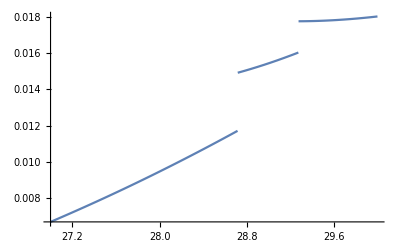

```mathematica
Plot[Piecewise[{{0, a < 23.25},{TakeupSideDiff[a* Pi /180,larm, xleader, yleader, xarm, yarm, rpulley],23.25 <= a < 28.717},
{TakeupSideDiff2[a* Pi /180,larm, xleader, yleader, xarm, yarm, rpulley],28.717 <= a < 29.275}, {TakeupSide[a* Pi /180,larm, xleader, yleader, xarm, yarm, rpulley], a ≥ 29.275}}], {a, 27, 30}]
```

```mathematica
{0.00603967705655431,{a->22.663838693845662}}
```

```mathematica
FindMinimum[TakeupSide[a* Pi /180,larm, xleader, yleader, xarm, yarm, rpulley], {a, 0}]
```

{0.0177527,{a→29.2575}}

```mathematica
deriveTakeup = Dt[TakeupSide[α[t],armlength, leaderx, leadery, armx,army, rpulley]] /. {Dt[t] -> 1, Dt[armlength] -> 0, Dt[leaderx] -> 0, Dt[leadery] -> 0, Dt[armx] -> 0, Dt[army] -> 0, Dt[rpulley] -> 0}
```

(-2 armlength (-armx+armlength Cos[α[t]]) Sin[α[t]] α'[t]+2 armlength Cos[α[t]] (-army+armlength Sin[α[t]]) α'[t])/(4 √(-0.0004+1/4 ((-armx+armlength Cos[α[t]])^2+(-army+armlength Sin[α[t]])^2)))+(-2 armlength (-armx+leaderx+armlength Cos[α[t]]) Sin[α[t]] α'[t]+2 armlength Cos[α[t]] (-army-leadery+armlength Sin[α[t]]) α'[t])/(4 √(-0.0004+1/4 ((-armx+leaderx+armlength Cos[α[t]])^2+(-army-leadery+armlength Sin[α[t]])^2)))+0.02 (-((0.02 (-2 armlength (-armx+leaderx+armlength Cos[α[t]]) Sin[α[t]] α'[t]+2 armlength Cos[α[t]] (-army-leadery+armlength Sin[α[t]]) α'[t]))/(((-armx+leaderx+armlength Cos[α[t]])^2+(-army-leadery+armlength Sin[α[t]])^2)^(3/2) √(1-0.0016/((-armx+leaderx+armlength Cos[α[t]])^2+(-army-leadery+armlength Sin[α[t]])^2))))-(-(armlength Sin[α[t]] α'[t])/(√((-armx+leaderx+armlength Cos[α[t]])^2+(-army-leadery+armlength Sin[α[t]])^2))-((-armx+leaderx+armlength Cos[α[t]]) (-2 armlength (-armx+leaderx+armlength Cos[α[t]]) Sin[α[t]] α'[t]+2 armlength Cos[α[t]] (-army-leadery+armlength Sin[α[t]]) α'[t]))/(2 ((-armx+leaderx+armlength Cos[α[t]])^2+(-army-leadery+armlength Sin[α[t]])^2)^(3/2)))/(√(1-(-armx+leaderx+armlength Cos[α[t]])^2/((-armx+leaderx+armlength Cos[α[t]])^2+(-army-leadery+armlength Sin[α[t]])^2))))+0.02 (-(0.02 (-2 armlength (-armx+armlength Cos[α[t]]) Sin[α[t]] α'[t]+2 armlength Cos[α[t]] (-army+armlength Sin[α[t]]) α'[t]))/(((-armx+armlength Cos[α[t]])^2+(-army+armlength Sin[α[t]])^2)^(3/2) √(1-0.0016/((-armx+armlength Cos[α[t]])^2+(-army+armlength Sin[α[t]])^2)))-(0.02 (-2 armlength (-armx+leaderx+armlength Cos[α[t]]) Sin[α[t]] α'[t]+2 armlength Cos[α[t]] (-army-leadery+armlength Sin[α[t]]) α'[t]))/(((-armx+leaderx+armlength Cos[α[t]])^2+(-army-leadery+armlength Sin[α[t]])^2)^(3/2) √(1-0.0016/((-armx+leaderx+armlength Cos[α[t]])^2+(-army-leadery+armlength Sin[α[t]])^2)))+(-(((-leaderx^2+(-armx+armlength Cos[α[t]])^2+(-armx+leaderx+armlength Cos[α[t]])^2+(-army+armlength Sin[α[t]])^2+(-army-leadery+armlength Sin[α[t]])^2) (-2 armlength (-armx+armlength Cos[α[t]]) Sin[α[t]] α'[t]+2 armlength Cos[α[t]] (-army+armlength Sin[α[t]]) α'[t]))/(4 ((-armx+armlength Cos[α[t]])^2+(-army+armlength Sin[α[t]])^2)^(3/2) √((-armx+leaderx+armlength Cos[α[t]])^2+(-army-leadery+armlength Sin[α[t]])^2)))-((-leaderx^2+(-armx+armlength Cos[α[t]])^2+(-armx+leaderx+armlength Cos[α[t]])^2+(-army+armlength Sin[α[t]])^2+(-army-leadery+armlength Sin[α[t]])^2) (-2 armlength (-armx+leaderx+armlength Cos[α[t]]) Sin[α[t]] α'[t]+2 armlength Cos[α[t]] (-army-leadery+armlength Sin[α[t]]) α'[t]))/(4 √((-armx+armlength Cos[α[t]])^2+(-army+armlength Sin[α[t]])^2) ((-armx+leaderx+armlength Cos[α[t]])^2+(-army-leadery+armlength Sin[α[t]])^2)^(3/2))+(-2 armlength (-armx+armlength Cos[α[t]]) Sin[α[t]] α'[t]-2 armlength (-armx+leaderx+armlength Cos[α[t]]) Sin[α[t]] α'[t]+2 armlength Cos[α[t]] (-army+armlength Sin[α[t]]) α'[t]+2 armlength Cos[α[t]] (-army-leadery+armlength Sin[α[t]]) α'[t])/(2 √((-armx+armlength Cos[α[t]])^2+(-army+armlength Sin[α[t]])^2) √((-armx+leaderx+armlength Cos[α[t]])^2+(-army-leadery+armlength Sin[α[t]])^2)))/(√(1-(-leaderx^2+(-armx+armlength Cos[α[t]])^2+(-armx+leaderx+armlength Cos[α[t]])^2+(-army+armlength Sin[α[t]])^2+(-army-leadery+armlength Sin[α[t]])^2)^2/(4 ((-armx+armlength Cos[α[t]])^2+(-army+armlength Sin[α[t]])^2) ((-armx+leaderx+armlength Cos[α[t]])^2+(-army-leadery+armlength Sin[α[t]])^2)))))

```mathematica
deriveTakeup /. {armlength -> larm, leaderx -> xleader, leadery -> yleader, armx -> xarm, army -> yarm, α[t] -> a, α'[t]->r}
```

(0.5 r Cos[a] (-0.11+0.25 Sin[a])-0.5 r (-0.3542+0.25 Cos[a]) Sin[a])/(4 √(-0.0004+1/4 ((-0.3542+0.25 Cos[a])^2+(-0.11+0.25 Sin[a])^2)))+(0.5 r Cos[a] (-0.125+0.25 Sin[a])-0.5 r (-0.1542+0.25 Cos[a]) Sin[a])/(4 √(-0.0004+1/4 ((-0.1542+0.25 Cos[a])^2+(-0.125+0.25 Sin[a])^2)))+0.02 (-(0.02 (0.5 r Cos[a] (-0.125+0.25 Sin[a])-0.5 r (-0.1542+0.25 Cos[a]) Sin[a]))/(√(1-0.0016/((-0.1542+0.25 Cos[a])^2+(-0.125+0.25 Sin[a])^2)) ((-0.1542+0.25 Cos[a])^2+(-0.125+0.25 Sin[a])^2)^(3/2))-(-(0.25 r Sin[a])/(√((-0.1542+0.25 Cos[a])^2+(-0.125+0.25 Sin[a])^2))-((-0.1542+0.25 Cos[a]) (0.5 r Cos[a] (-0.125+0.25 Sin[a])-0.5 r (-0.1542+0.25 Cos[a]) Sin[a]))/(2 ((-0.1542+0.25 Cos[a])^2+(-0.125+0.25 Sin[a])^2)^(3/2)))/(√(1-(-0.1542+0.25 Cos[a])^2/((-0.1542+0.25 Cos[a])^2+(-0.125+0.25 Sin[a])^2))))+0.02 (-(0.02 (0.5 r Cos[a] (-0.11+0.25 Sin[a])-0.5 r (-0.3542+0.25 Cos[a]) Sin[a]))/(√(1-0.0016/((-0.3542+0.25 Cos[a])^2+(-0.11+0.25 Sin[a])^2)) ((-0.3542+0.25 Cos[a])^2+(-0.11+0.25 Sin[a])^2)^(3/2))-(0.02 (0.5 r Cos[a] (-0.125+0.25 Sin[a])-0.5 r (-0.1542+0.25 Cos[a]) Sin[a]))/(√(1-0.0016/((-0.1542+0.25 Cos[a])^2+(-0.125+0.25 Sin[a])^2)) ((-0.1542+0.25 Cos[a])^2+(-0.125+0.25 Sin[a])^2)^(3/2))+(-(((-0.04+(-0.3542+0.25 Cos[a])^2+(-0.1542+0.25 Cos[a])^2+(-0.125+0.25 Sin[a])^2+(-0.11+0.25 Sin[a])^2) (0.5 r Cos[a] (-0.11+0.25 Sin[a])-0.5 r (-0.3542+0.25 Cos[a]) Sin[a]))/(4 √((-0.1542+0.25 Cos[a])^2+(-0.125+0.25 Sin[a])^2) ((-0.3542+0.25 Cos[a])^2+(-0.11+0.25 Sin[a])^2)^(3/2)))-((-0.04+(-0.3542+0.25 Cos[a])^2+(-0.1542+0.25 Cos[a])^2+(-0.125+0.25 Sin[a])^2+(-0.11+0.25 Sin[a])^2) (0.5 r Cos[a] (-0.125+0.25 Sin[a])-0.5 r (-0.1542+0.25 Cos[a]) Sin[a]))/(4 ((-0.1542+0.25 Cos[a])^2+(-0.125+0.25 Sin[a])^2)^(3/2) √((-0.3542+0.25 Cos[a])^2+(-0.11+0.25 Sin[a])^2))+(0.5 r Cos[a] (-0.125+0.25 Sin[a])+0.5 r Cos[a] (-0.11+0.25 Sin[a])-0.5 r (-0.3542+0.25 Cos[a]) Sin[a]-0.5 r (-0.1542+0.25 Cos[a]) Sin[a])/(2 √((-0.1542+0.25 Cos[a])^2+(-0.125+0.25 Sin[a])^2) √((-0.3542+0.25 Cos[a])^2+(-0.11+0.25 Sin[a])^2)))/(√(1-((-0.04+(-0.3542+0.25 Cos[a])^2+(-0.1542+0.25 Cos[a])^2+(-0.125+0.25 Sin[a])^2+(-0.11+0.25 Sin[a])^2)^2)/(4 ((-0.1542+0.25 Cos[a])^2+(-0.125+0.25 Sin[a])^2) ((-0.3542+0.25 Cos[a])^2+(-0.11+0.25 Sin[a])^2)))))

```mathematica
deriveTakeup /. {armlength -> larm, leaderx -> xleader, leadery -> yleader, armx -> xarm, army -> yarm, α[t] -> 1.4549999999999506, α'[t]->0}
```

0.

```mathematica
TakeupSide[a,larm, xleader, yleader, xarm, yarm, rpulley]
```

-0.2+0.02 (2 π-ArcCos[0.04/(√((-0.1542+0.25 Cos[a])^2+(-0.125+0.25 Sin[a])^2))]-ArcCos[0.04/(√((-0.3542+0.25 Cos[a])^2+(-0.11+0.25 Sin[a])^2))]-ArcCos[(-0.04+(-0.3542+0.25 Cos[a])^2+(-0.1542+0.25 Cos[a])^2+(-0.125+0.25 Sin[a])^2+(-0.11+0.25 Sin[a])^2)/(2 √((-0.1542+0.25 Cos[a])^2+(-0.125+0.25 Sin[a])^2) √((-0.3542+0.25 Cos[a])^2+(-0.11+0.25 Sin[a])^2))])+0.02 (π-ArcCos[0.04/(√((-0.1542+0.25 Cos[a])^2+(-0.125+0.25 Sin[a])^2))]-ArcSin[(-0.1542+0.25 Cos[a])/(√((-0.1542+0.25 Cos[a])^2+(-0.125+0.25 Sin[a])^2))])+2 √(-0.0004+1/4 ((-0.1542+0.25 Cos[a])^2+(-0.125+0.25 Sin[a])^2))+2 √(-0.0004+1/4 ((-0.3542+0.25 Cos[a])^2+(-0.11+0.25 Sin[a])^2))

```mathematica
FullSimplify[Takeup[α,β, Subscript[l, arm], Subscript[x, leader], Subscript[y, leader], Subscript[x, arm], Subscript[y, arm], Subscript[r, pulley]]]
```

(2 π+ArcSin[(2 r_pulley)/(√((-Cos[α] l_arm+x_arm)^2+(-Sin[α] l_arm+y_arm)^2))]+ArcSin[(2 r_pulley)/(√((-Cos[β] l_arm+x_arm)^2+(-Sin[β] l_arm+y_arm)^2))]+2 ArcSin[(2 r_pulley)/(√((Cos[α] l_arm-x_arm+x_leader)^2+(-Sin[α] l_arm+y_arm+y_leader)^2))]-ArcSin[(Cos[α] l_arm-x_arm+x_leader)/(√((Cos[α] l_arm-x_arm+x_leader)^2+(-Sin[α] l_arm+y_arm+y_leader)^2))]+ArcSin[((-Cos[α] l_arm+x_arm)^2-x_leader^2+(Cos[α] l_arm-x_arm+x_leader)^2+(-Sin[α] l_arm+y_arm)^2+(-Sin[α] l_arm+y_arm+y_leader)^2)/(2 √((-Cos[α] l_arm+x_arm)^2+(-Sin[α] l_arm+y_arm)^2) √((Cos[α] l_arm-x_arm+x_leader)^2+(-Sin[α] l_arm+y_arm+y_leader)^2))]+2 ArcSin[(2 r_pulley)/(√((Cos[β] l_arm-x_arm+x_leader)^2+(-Sin[β] l_arm+y_arm+y_leader)^2))]-ArcSin[(Cos[β] l_arm-x_arm+x_leader)/(√((Cos[β] l_arm-x_arm+x_leader)^2+(-Sin[β] l_arm+y_arm+y_leader)^2))]+ArcSin[((-Cos[β] l_arm+x_arm)^2-x_leader^2+(Cos[β] l_arm-x_arm+x_leader)^2+(-Sin[β] l_arm+y_arm)^2+(-Sin[β] l_arm+y_arm+y_leader)^2)/(2 √((-Cos[β] l_arm+x_arm)^2+(-Sin[β] l_arm+y_arm)^2) √((Cos[β] l_arm-x_arm+x_leader)^2+(-Sin[β] l_arm+y_arm+y_leader)^2))]) r_pulley-2 x_leader+√(l_arm^2-4 r_pulley^2+x_arm^2+y_arm^2-2 l_arm (Cos[α] x_arm+Sin[α] y_arm))+√(l_arm^2-4 r_pulley^2+x_arm^2+y_arm^2-2 l_arm (Cos[β] x_arm+Sin[β] y_arm))+√(-4 r_pulley^2+(Cos[α] l_arm-x_arm+x_leader)^2+(-Sin[α] l_arm+y_arm+y_leader)^2)+√(-4 r_pulley^2+(Cos[β] l_arm-x_arm+x_leader)^2+(-Sin[β] l_arm+y_arm+y_leader)^2)

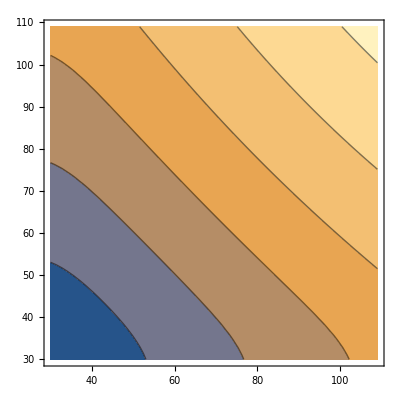

```mathematica
ContourPlot[Takeup[a * Pi /180,b * Pi / 180,larm, xleader, yleader, xarm, yarm, rpulley] , {a, 30, 109}, {b, 30, 109}]
```

```mathematica
Solve[(2 π+ArcSin[(2 Subscript[r, pulley])/(√((-Cos[α] Subscript[l, arm]+Subscript[x, arm])^2+(-Sin[α] Subscript[l, arm]+Subscript[y, arm])^2))]+ArcSin[(2 Subscript[r, pulley])/(√((-Cos[β] Subscript[l, arm]+Subscript[x, arm])^2+(-Sin[β] Subscript[l, arm]+Subscript[y, arm])^2))]+2 ArcSin[(2 Subscript[r, pulley])/(√((Cos[α] Subscript[l, arm]-Subscript[x, arm]+Subscript[x, leader])^2+(-Sin[α] Subscript[l, arm]+Subscript[y, arm]+Subscript[y, leader])^2))]-ArcSin[(Cos[α] Subscript[l, arm]-Subscript[x, arm]+Subscript[x, leader])/(√((Cos[α] Subscript[l, arm]-Subscript[x, arm]+Subscript[x, leader])^2+(-Sin[α] Subscript[l, arm]+Subscript[y, arm]+Subscript[y, leader])^2))]+ArcSin[((-Cos[α] Subscript[l, arm]+Subscript[x, arm])^2-Subscript[x, leader]^2+(Cos[α] Subscript[l, arm]-Subscript[x, arm]+Subscript[x, leader])^2+(-Sin[α] Subscript[l, arm]+Subscript[y, arm])^2+(-Sin[α] Subscript[l, arm]+Subscript[y, arm]+Subscript[y, leader])^2)/(2 √((-Cos[α] Subscript[l, arm]+Subscript[x, arm])^2+(-Sin[α] Subscript[l, arm]+Subscript[y, arm])^2) √((Cos[α] Subscript[l, arm]-Subscript[x, arm]+Subscript[x, leader])^2+(-Sin[α] Subscript[l, arm]+Subscript[y, arm]+Subscript[y, leader])^2))]+2 ArcSin[(2 Subscript[r, pulley])/(√((Cos[β] Subscript[l, arm]-Subscript[x, arm]+Subscript[x, leader])^2+(-Sin[β] Subscript[l, arm]+Subscript[y, arm]+Subscript[y, leader])^2))]-ArcSin[(Cos[β] Subscript[l, arm]-Subscript[x, arm]+Subscript[x, leader])/(√((Cos[β] Subscript[l, arm]-Subscript[x, arm]+Subscript[x, leader])^2+(-Sin[β] Subscript[l, arm]+Subscript[y, arm]+Subscript[y, leader])^2))]+ArcSin[((-Cos[β] Subscript[l, arm]+Subscript[x, arm])^2-Subscript[x, leader]^2+(Cos[β] Subscript[l, arm]-Subscript[x, arm]+Subscript[x, leader])^2+(-Sin[β] Subscript[l, arm]+Subscript[y, arm])^2+(-Sin[β] Subscript[l, arm]+Subscript[y, arm]+Subscript[y, leader])^2)/(2 √((-Cos[β] Subscript[l, arm]+Subscript[x, arm])^2+(-Sin[β] Subscript[l, arm]+Subscript[y, arm])^2) √((Cos[β] Subscript[l, arm]-Subscript[x, arm]+Subscript[x, leader])^2+(-Sin[β] Subscript[l, arm]+Subscript[y, arm]+Subscript[y, leader])^2))]) Subscript[r, pulley]-2 Subscript[x, leader]+√(Subscript[l, arm]^2-4 Subscript[r, pulley]^2+Subscript[x, arm]^2+Subscript[y, arm]^2-2 Subscript[l, arm] (Cos[α] Subscript[x, arm]+Sin[α] Subscript[y, arm]))+√(Subscript[l, arm]^2-4 Subscript[r, pulley]^2+Subscript[x, arm]^2+Subscript[y, arm]^2-2 Subscript[l, arm] (Cos[β] Subscript[x, arm]+Sin[β] Subscript[y, arm]))+√(-4 Subscript[r, pulley]^2+(Cos[α] Subscript[l, arm]-Subscript[x, arm]+Subscript[x, leader])^2+(-Sin[α] Subscript[l, arm]+Subscript[y, arm]+Subscript[y, leader])^2)+√(-4 Subscript[r, pulley]^2+(Cos[β] Subscript[l, arm]-Subscript[x, arm]+Subscript[x, leader])^2+(-Sin[β] Subscript[l, arm]+Subscript[y, arm]+Subscript[y, leader])^2)== Subscript[l, takeup] /. {β -> 0}, α]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[(2 π+ArcSin[(2 r_pulley)/(√((-l_arm+x_arm)^2+y_arm^2))]+ArcSin[(2 r_pulley)/(√((-Cos[α] l_arm+x_arm)^2+(-Sin[α] l_arm+y_arm)^2))]+2 ArcSin[(2 r_pulley)/(√((l_arm-x_arm+x_leader)^2+(y_arm+y_leader)^2))]-ArcSin[(l_arm-x_arm+x_leader)/(√((l_arm-x_arm+x_leader)^2+(y_arm+y_leader)^2))]+ArcSin[((-l_arm+x_arm)^2-x_leader^2+(l_arm-x_arm+x_leader)^2+y_arm^2+(y_arm+y_leader)^2)/(2 √((-l_arm+x_arm)^2+y_arm^2) √((l_arm-x_arm+x_leader)^2+(y_arm+y_leader)^2))]+2 ArcSin[(2 r_pulley)/(√((Cos[α] l_arm-x_arm+x_leader)^2+(-Sin[α] l_arm+y_arm+y_leader)^2))]-ArcSin[(Cos[α] l_arm-x_arm+x_leader)/(√((Cos[α] l_arm-x_arm+x_leader)^2+(-Sin[α] l_arm+y_arm+y_leader)^2))]+ArcSin[((-Cos[α] l_arm+x_arm)^2-x_leader^2+(Cos[α] l_arm-x_arm+x_leader)^2+(-Sin[α] l_arm+y_arm)^2+(-Sin[α] l_arm+y_arm+y_leader)^2)/(2 √((-Cos[α] l_arm+x_arm)^2+(-Sin[α] l_arm+y_arm)^2) √((Cos[α] l_arm-x_arm+x_leader)^2+(-Sin[α] l_arm+y_arm+y_leader)^2))]) r_pulley-2 x_leader+√(l_arm^2-4 r_pulley^2-2 l_arm x_arm+x_arm^2+y_arm^2)+√(l_arm^2-4 r_pulley^2+x_arm^2+y_arm^2-2 l_arm (Cos[α] x_arm+Sin[α] y_arm))+√(-4 r_pulley^2+(l_arm-x_arm+x_leader)^2+(y_arm+y_leader)^2)+√(-4 r_pulley^2+(Cos[α] l_arm-x_arm+x_leader)^2+(-Sin[α] l_arm+y_arm+y_leader)^2)==l_takeup,α]

```mathematica
CForm[(2 π+ArcSin[(2 Subscript[r, pulley])/(√((-Cos[α] Subscript[l, arm]+Subscript[x, arm])^2+(-Sin[α] Subscript[l, arm]+Subscript[y, arm])^2))]+ArcSin[(2 Subscript[r, pulley])/(√((-Cos[β] Subscript[l, arm]+Subscript[x, arm])^2+(-Sin[β] Subscript[l, arm]+Subscript[y, arm])^2))]+2 ArcSin[(2 Subscript[r, pulley])/(√((Cos[α] Subscript[l, arm]-Subscript[x, arm]+Subscript[x, leader])^2+(-Sin[α] Subscript[l, arm]+Subscript[y, arm]+Subscript[y, leader])^2))]-ArcSin[(Cos[α] Subscript[l, arm]-Subscript[x, arm]+Subscript[x, leader])/(√((Cos[α] Subscript[l, arm]-Subscript[x, arm]+Subscript[x, leader])^2+(-Sin[α] Subscript[l, arm]+Subscript[y, arm]+Subscript[y, leader])^2))]+ArcSin[((-Cos[α] Subscript[l, arm]+Subscript[x, arm])^2-Subscript[x, leader]^2+(Cos[α] Subscript[l, arm]-Subscript[x, arm]+Subscript[x, leader])^2+(-Sin[α] Subscript[l, arm]+Subscript[y, arm])^2+(-Sin[α] Subscript[l, arm]+Subscript[y, arm]+Subscript[y, leader])^2)/(2 √((-Cos[α] Subscript[l, arm]+Subscript[x, arm])^2+(-Sin[α] Subscript[l, arm]+Subscript[y, arm])^2) √((Cos[α] Subscript[l, arm]-Subscript[x, arm]+Subscript[x, leader])^2+(-Sin[α] Subscript[l, arm]+Subscript[y, arm]+Subscript[y, leader])^2))]+2 ArcSin[(2 Subscript[r, pulley])/(√((Cos[β] Subscript[l, arm]-Subscript[x, arm]+Subscript[x, leader])^2+(-Sin[β] Subscript[l, arm]+Subscript[y, arm]+Subscript[y, leader])^2))]-ArcSin[(Cos[β] Subscript[l, arm]-Subscript[x, arm]+Subscript[x, leader])/(√((Cos[β] Subscript[l, arm]-Subscript[x, arm]+Subscript[x, leader])^2+(-Sin[β] Subscript[l, arm]+Subscript[y, arm]+Subscript[y, leader])^2))]+ArcSin[((-Cos[β] Subscript[l, arm]+Subscript[x, arm])^2-Subscript[x, leader]^2+(Cos[β] Subscript[l, arm]-Subscript[x, arm]+Subscript[x, leader])^2+(-Sin[β] Subscript[l, arm]+Subscript[y, arm])^2+(-Sin[β] Subscript[l, arm]+Subscript[y, arm]+Subscript[y, leader])^2)/(2 √((-Cos[β] Subscript[l, arm]+Subscript[x, arm])^2+(-Sin[β] Subscript[l, arm]+Subscript[y, arm])^2) √((Cos[β] Subscript[l, arm]-Subscript[x, arm]+Subscript[x, leader])^2+(-Sin[β] Subscript[l, arm]+Subscript[y, arm]+Subscript[y, leader])^2))]) Subscript[r, pulley]-2 Subscript[x, leader]+√(Subscript[l, arm]^2-4 Subscript[r, pulley]^2+Subscript[x, arm]^2+Subscript[y, arm]^2-2 Subscript[l, arm] (Cos[α] Subscript[x, arm]+Sin[α] Subscript[y, arm]))+√(Subscript[l, arm]^2-4 Subscript[r, pulley]^2+Subscript[x, arm]^2+Subscript[y, arm]^2-2 Subscript[l, arm] (Cos[β] Subscript[x, arm]+Sin[β] Subscript[y, arm]))+√(-4 Subscript[r, pulley]^2+(Cos[α] Subscript[l, arm]-Subscript[x, arm]+Subscript[x, leader])^2+(-Sin[α] Subscript[l, arm]+Subscript[y, arm]+Subscript[y, leader])^2)+√(-4 Subscript[r, pulley]^2+(Cos[β] Subscript[l, arm]-Subscript[x, arm]+Subscript[x, leader])^2+(-Sin[β] Subscript[l, arm]+Subscript[y, arm]+Subscript[y, leader])^2) /. {Subscript[r, pulley] -> rPulley, Subscript[l, arm] -> armLength, Subscript[y, arm]-> armHeight, Subscript[y, leader]-> leaderPulleyHeight, Subscript[x, arm]-> armDist, Subscript[x, leader] -> leaderPulleyDist, α -> rightArmAngle, β -> leftArmAngle}]
```

-2*leaderPulleyDist + rPulley*(2*Pi + ArcSin((2*rPulley)/
        Sqrt(Power(armDist - armLength*Cos(leftArmAngle),2) + Power(armHeight - armLength*Sin(leftArmAngle),2))) + 
      2*ArcSin((2*rPulley)/Sqrt(Power(-armDist + leaderPulleyDist + armLength*Cos(leftArmAngle),2) + 
           Power(armHeight + leaderPulleyHeight - armLength*Sin(leftArmAngle),2))) - 
      ArcSin((-armDist + leaderPulleyDist + armLength*Cos(leftArmAngle))/
        Sqrt(Power(-armDist + leaderPulleyDist + armLength*Cos(leftArmAngle),2) + 
          Power(armHeight + leaderPulleyHeight - armLength*Sin(leftArmAngle),2))) + 
      ArcSin((-Power(leaderPulleyDist,2) + Power(armDist - armLength*Cos(leftArmAngle),2) + 
          Power(-armDist + leaderPulleyDist + armLength*Cos(leftArmAngle),2) + Power(armHeight - armLength*Sin(leftArmAngle),2) + 
          Power(armHeight + leaderPulleyHeight - armLength*Sin(leftArmAngle),2))/
        (2.*Sqrt(Power(armDist - armLength*Cos(leftArmAngle),2) + Power(armHeight - armLength*Sin(leftArmAngle),2))*
          Sqrt(Power(-armDist + leaderPulleyDist + armLength*Cos(leftArmAngle),2) + 
            Power(armHeight + leaderPulleyHeight - armLength*Sin(leftArmAngle),2)))) + 
      ArcSin((2*rPulley)/Sqrt(Power(armDist - armLength*Cos(rightArmAngle),2) + Power(armHeight - armLength*Sin(rightArmAngle),2))) + 
      2*ArcSin((2*rPulley)/Sqrt(Power(-armDist + leaderPulleyDist + armLength*Cos(rightArmAngle),2) + 
           Power(armHeight + leaderPulleyHeight - armLength*Sin(rightArmAngle),2))) - 
      ArcSin((-armDist + leaderPulleyDist + armLength*Cos(rightArmAngle))/
        Sqrt(Power(-armDist + leaderPulleyDist + armLength*Cos(rightArmAngle),2) + 
          Power(armHeight + leaderPulleyHeight - armLength*Sin(rightArmAngle),2))) + 
      ArcSin((-Power(leaderPulleyDist,2) + Power(armDist - armLength*Cos(rightArmAngle),2) + 
          Power(-armDist + leaderPulleyDist + armLength*Cos(rightArmAngle),2) + Power(armHeight - armLength*Sin(rightArmAngle),2) + 
          Power(armHeight + leaderPulleyHeight - armLength*Sin(rightArmAngle),2))/
        (2.*Sqrt(Power(armDist - armLength*Cos(rightArmAngle),2) + Power(armHeight - armLength*Sin(rightArmAngle),2))*
          Sqrt(Power(-armDist + leaderPulleyDist + armLength*Cos(rightArmAngle),2) + 
            Power(armHeight + leaderPulleyHeight - armLength*Sin(rightArmAngle),2))))) + 
   Sqrt(Power(armDist,2) + Power(armHeight,2) + Power(armLength,2) - 4*Power(rPulley,2) - 
     2*armLength*(armDist*Cos(leftArmAngle) + armHeight*Sin(leftArmAngle))) + 
   Sqrt(-4*Power(rPulley,2) + Power(-armDist + leaderPulleyDist + armLength*Cos(leftArmAngle),2) + 
     Power(armHeight + leaderPulleyHeight - armLength*Sin(leftArmAngle),2)) + 
   Sqrt(Power(armDist,2) + Power(armHeight,2) + Power(armLength,2) - 4*Power(rPulley,2) - 
     2*armLength*(armDist*Cos(rightArmAngle) + armHeight*Sin(rightArmAngle))) + 
   Sqrt(-4*Power(rPulley,2) + Power(-armDist + leaderPulleyDist + armLength*Cos(rightArmAngle),2) + 
     Power(armHeight + leaderPulleyHeight - armLength*Sin(rightArmAngle),2))

```mathematica
CForm[TakeupSide[armAngle, armLength, leaderPulleyX, leaderPulleyY, armX, armY, rPulley]]
```

-leaderPulleyX + rPulley*(2*Pi - ArcCos((2*rPulley)/Sqrt(Power(-armX + armLength*Cos(armAngle),2) + Power(-armY + armLength*Sin(armAngle),2))) - 
      ArcCos((2*rPulley)/Sqrt(Power(-armX + leaderPulleyX + armLength*Cos(armAngle),2) + 
          Power(-armY - leaderPulleyY + armLength*Sin(armAngle),2))) - 
      ArcCos((-Power(leaderPulleyX,2) + Power(-armX + armLength*Cos(armAngle),2) + Power(-armX + leaderPulleyX + armLength*Cos(armAngle),2) + 
          Power(-armY + armLength*Sin(armAngle),2) + Power(-armY - leaderPulleyY + armLength*Sin(armAngle),2))/
        (2.*Sqrt(Power(-armX + armLength*Cos(armAngle),2) + Power(-armY + armLength*Sin(armAngle),2))*
          Sqrt(Power(-armX + leaderPulleyX + armLength*Cos(armAngle),2) + Power(-armY - leaderPulleyY + armLength*Sin(armAngle),2))))) + 
   rPulley*(Pi - ArcCos((2*rPulley)/
        Sqrt(Power(-armX + leaderPulleyX + armLength*Cos(armAngle),2) + Power(-armY - leaderPulleyY + armLength*Sin(armAngle),2))) - 
      ArcSin((-armX + leaderPulleyX + armLength*Cos(armAngle))/
        Sqrt(Power(-armX + leaderPulleyX + armLength*Cos(armAngle),2) + Power(-armY - leaderPulleyY + armLength*Sin(armAngle),2)))) + 
   2*Sqrt(-Power(rPulley,2) + (Power(-armX + armLength*Cos(armAngle),2) + Power(-armY + armLength*Sin(armAngle),2))/4.) + 
   2*Sqrt(-Power(rPulley,2) + (Power(-armX + leaderPulleyX + armLength*Cos(armAngle),2) + 
         Power(-armY - leaderPulleyY + armLength*Sin(armAngle),2))/4.)